```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
tvalue=0.4;
mub=9.27*10^(-24)*(10^19/1.6)*1000/600(**Bohr magneton=9.27*10^(-24)JT^(-1)**);
bvaluedat={0,75,150,200,300,500,600,700,900};
```

```mathematica
momentax=Table[Total[Flatten[ Import[StringJoin["trot_",ToString[tvalue],"_allmtax_",ToString[bvalue],"sq2.dat"]][[1]][[{1,5,9}]]]],{bvalue,bvaluedat}];
momentbx=Table[Total[Flatten[ Import[StringJoin["trot_",ToString[tvalue],"_allmtbx_",ToString[bvalue],"sq2.dat"]][[1]][[{1,5,9}]]]],{bvalue,bvaluedat}];

mgdata=Table[{bvaluedat[[i]]*Sqrt[2]*mub/0.5,((momentax+momentbx)/2)[[i]]},{i,1,Length[bvaluedat]}];
```

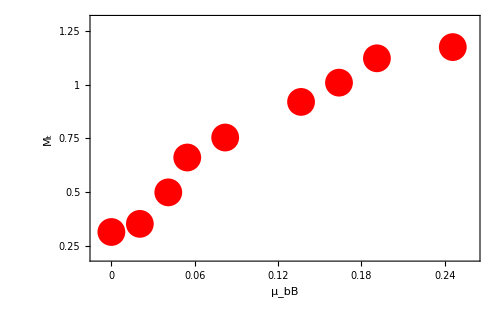

```mathematica
mgplot=ListPlot[mgdata,Frame->True,FrameStyle->Directive[Thickness[0.005],Black,32],Epilog->{{Red,PointSize[0.04],Point[mgdata]}},PlotRange->{{-0.01,0.26},{0.2,1.3}},
FrameTicks->{{{{0.25,0.25,0.03},{0.5,0.5,0.03},{0.75,0.75,0.03},{1,1,0.03},{1.25,1.25,0.03}},{{0.25,Null,0.03},{0.5,Null,0.03},{0.75,Null,0.03},{1,Null,0.03},{1.25,Null,0.03}}},{{{0,0,0.03},{0.06,0.06,0.03},{0.12,0.12,0.03},{0.18,0.18,0.03},{0.24,0.24,0.03}},{{0,Null,0.03},{0.06,Null,0.03},{0.12,Null,0.03},{0.18,Null,0.03},{0.24,Null,0.03}}}},
FrameLabel->{{Style["M_t",35,FontFamily->"TimesNewRoman"],None},{Style["μ_bB",35,FontFamily->"TimesNewRoman"],None}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,35]},
ImagePadding->{{110,25},{90,17}},ImageSize->500]
Export["mgplot.eps",mgplot];
```